```mathematica
(* Check well knoen mountaineers theorem: during a full moon it is often good weather
Short answer: NO
*)
```

InterpolatingFunction::dmval: Input value {3680467200} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3680553600} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3680640000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

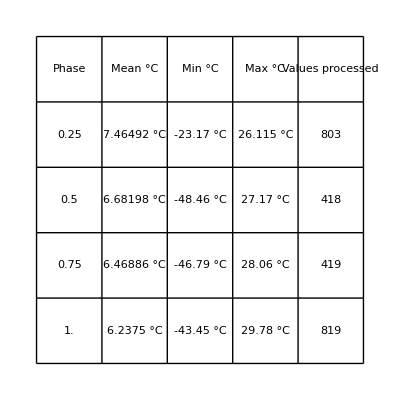

```mathematica
days={"2010-01-01", "2016-10-20", "Day"};
getMoons[d_]:=getMoons[d]=MoonPhase[d];
moons=getMoons[days];
temps=WeatherData[{39.3481331,72.8760069}, "Temperature", days];
data = TimeSeriesThread[Function[a, a], {moons, temps}];
values = GroupBy[data[[2]][[1]][[1]], Ceiling[#[[1]], 0.25]&];
values = KeyValueMap[Function[{k,v}, {k,Map[Last,v]}],values];
makeStat[v_]:=(
phase=v[[1]];
vs=v[[2]];
filtered=Select[vs, # > Quantity[-50, "DegreesCelsius"] && # < Quantity[50, "DegreesCelsius"]&];
{phase, Mean[filtered], Min[filtered], Max[filtered], Length[filtered]}
);
stat = SortBy[makeStat /@ values, First];
GraphicsGrid[Join[{{"Phase", "Mean °C", "Min °C", "Max °C", "Values processed"}}, stat], Frame->All]
```